# Minimal Keller–Segel system with logistic growth

In this notebook, we consider the minimal Keller–Segel model defined by χ_ρ=χ_c=1 and f=ρ-c with the logistic source term s(ρ)=ρ (p-ρ).
We first solve the analytical expressions for the thresholds of interrupted coarsening and plateau splitting for this model.
Then, these thresholds are determined numerically using pseudo-arclength continuation to calculate the stationary patterns within a finite-differences approximation and their stability:
The threshold of interrupted coarsening corresponds to a change in stability of the symmetric stationary pattern while the threshold of plateau splitting corresponds to a fold bifurcation of the elementary stationary pattern.
Comparison of the numerical results with the theoretical analysis verifies the threshold expressions.

For pseudo-arclength continuation, we adopt the code previously employed for two-component (mass-conserving) reaction–diffusion systems in Ref. Brauns, et al., Wavelength selection by interrupted coarsening in reaction–diffusion systems, PRL 126(10), 104101.

Because the lower plateau density ρ_- approaches zero quickly for large peak masses, in the numerical finite-differences analysis, we parameterize the patterns by a=Log[ρ], which has a smoother profile.
This allows one to find the stationary profile, in particular the profile in the pattern plateaus relevant for the mass-competition rate, with higher accuracy.

## Setup

```mathematica
params={Dc->1,Dρ->0.1,T->5,ϵ->10^-3,L->8,p->1,time->10^10};
```

```mathematica
f=(η-(Dρ/T Log[ρ]- ρ));
```

#### Nullcline

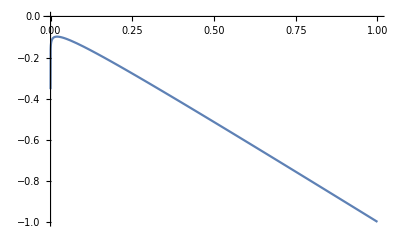

```mathematica
Plot[(Dρ/T Log[ρ]- ρ)/.params,{ρ,0,1}]
```

## System with source term

#### Setup of PDE simulation

```mathematica
ClearAll@runKSSim;
Options[runKSSim]=Join[Options[NDSolve],{"GridPoints"->300,"BC"->"Reflective"}];
runKSSim[params_,{ρInit_,cInit_},tMax_,opts:OptionsPattern[]]:=First@NDSolve[{
D[ρ[x,t],t]==Dρ*D[ρ[x,t],{x,2}]-T*D[ρ[x,t]*D[c[x,t],x],x]+ϵ*ρ[x,t]*(p-ρ[x,t]),D[c[x,t],t]==Dc*D[c[x,t],{x,2}]+ρ[x,t]-c[x,t],
If[OptionValue["BC"]==="Periodic",
{(* periodic BCs *)
ρ[0,t]==ρ[L,t],c[0,t]==c[L,t],
(D[ρ[x,t],x]/.x->0)==(D[ρ[x,t],x]/.x->L),(D[c[x,t],x]/.x->0)==(D[c[x,t],x]/.x->L)
},
{(* reflective BCs*)
(D[ρ[x,t],x]/.x->0)==0,(D[ρ[x,t],x]/.x->L)==0,
(D[c[x,t],x]/.x->0)==0,(D[c[x,t],x]/.x->L)==0
}],
(* initial condition *)
ρ[x,0]==ρInit[x],
c[x,0]==cInit[x]
}/.params,
{ρ,c},
{x,0,L/.params},
{t,0,tMax},
Evaluate[Sequence@@FilterRules[List@opts,Options[NDSolve]]],Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->OptionValue["GridPoints"],"MaxPoints"->OptionValue["GridPoints"],AccuracyGoal->0,PrecisionGoal->0,"DifferenceOrder"->2},"DifferentiateBoundaryConditions"->{True,"ScaleFactor"->2},"Method"->{"IDA","ImplicitSolver"->"Newton"}}
];
```

#### Setup finite-difference equations for the stationary state

```mathematica
discreteLaplace[data_,dx_]:=With[{paddedData=Join[{data[[1]]},data,{data[[-1]]}]},
Differences[paddedData,2]/dx^2
]
```

```mathematica
discreteGradient[data_,dx_]:=With[{paddedData=Join[{data[[1]]},data,{data[[-1]]}]},
Differences[paddedData,1,2]/(2dx)
]
```

```mathematica
ClearAll@setupFiniteDifferenceEqs;
setupFiniteDifferenceEqs[gridRes_]:=With[{
aVec=Thread[a@Range[gridRes]],
cVec=Thread[c@Range[gridRes]]
},
<|
"UnitGrid"->Range[0.5/gridRes,1,1./gridRes],
"aVec"->aVec,
"cVec"->cVec,
"Vars"->Join[aVec,cVec],
"Eqs"->{
T(discreteGradient[aVec,L/gridRes]*discreteGradient[Dρ/T aVec-cVec,L/gridRes] +discreteLaplace[Dρ/T aVec-cVec,L/gridRes]) +(ϵ(p-ρ)/.{ρ->Exp[aVec]}),
Dc  discreteLaplace[cVec,L/gridRes]+Exp[aVec]-cVec
}
|>
]
```

```mathematica
getInitGuess[fdSetup_,params_,initSol_]:=Join[
Transpose[{
fdSetup["aVec"],
Log[ρ[x,time]]/.params/.initSol/.x->(L/.params) fdSetup["UnitGrid"]
}],
Transpose[{
fdSetup["cVec"],
c[x,time]/.params/.initSol/.x->(L/.params) fdSetup["UnitGrid"]
}]
]
```

#### Jacobian

Construct the Jacobian (linear dynamic matrix) of the linear dynamics around the stationary pattern.
The Kronecker product is used to build the interleaved matrix for the components of a and c: For the discrete domain points x1, x2, x3, ... (stemming from the discretization of a single elementary pattern, e.g., the domain [0, Lambda/2]), the constructed interleaved Jacobian matrix describes the dynamics of the vector [a(x1),c(x1),a(x2),c(x2),...].
Importantly, the dynamics is determined only on the right half-domain of the symmetric stationary pattern because the dynamics in the left part of the domain follows from the required symmetry or antisymmetry of the eigenmodes.

Discretized Laplacian (using central differences) with no-flux boundaries (laplaceMatrixS; for symmetric eigenmodes/profiles) and with one Dirichlet boundary and one no-flux boundary (laplaceMatrixAS; for antisymmetric eigenmodes/profiles):

```mathematica
laplaceMatrixS[n_]:=SparseArray[{
{1,1}->-1,{-1,-1}->-1,
{i_,i_}->-2,
{i_,j_}/;Abs[i-j]==1->1
},
{n,n}
]
laplaceMatrixAS[n_]:=SparseArray[{
{1,1}->-1,{-1,-1}->-3,
{i_,i_}->-2,
{i_,j_}/;Abs[i-j]==1->1
},
{n,n}
]
```

The corresponding matrix approximations of the gradient:

```mathematica
gradMatrixS[n_]:=SparseArray[{
{1,1}->-1,{-1,-1}->1,
{i_,j_}/;(i-j)==1->-1,
{i_,j_}/;(i-j)==-1->1
},
{n,n}
]/2
gradMatrixAS[n_]:=SparseArray[{
{1,1}->-1,{-1,-1}->-1,
{i_,j_}/;(i-j)==1->-1,
{i_,j_}/;(i-j)==-1->1
},
{n,n}
]/2
```

```mathematica
ClearAll@constructGluedJacobian;
Options@constructGluedJacobian={"Reverse"->False,"Symmetric"->False};
constructGluedJacobian[fdSetup_,params_,statSol_,OptionsPattern[]]:=
Block[{
solVec=If[OptionValue["Reverse"]===True,Reverse@#,#]&@Transpose[{
fdSetup["aVec"]/.statSol,
fdSetup["cVec"]/.statSol
}],
gridRes=Length@fdSetup["UnitGrid"],
grid
},
KroneckerProduct[DiagonalMatrix[discreteGradient[(2Dρ/T)solVec[[All,1]]-solVec[[All,2]],1]].If[OptionValue["Symmetric"]===True,gradMatrixS,gradMatrixAS][gridRes]+Dρ/T If[OptionValue["Symmetric"]===True,laplaceMatrixS,laplaceMatrixAS][gridRes],{{T,0},{0,0}}/(L/gridRes)^2/.params]+KroneckerProduct[If[OptionValue["Symmetric"]===True,laplaceMatrixS,laplaceMatrixAS][gridRes]+DiagonalMatrix[discreteGradient[solVec[[All,1]],1]].If[OptionValue["Symmetric"]===True,gradMatrixS,gradMatrixAS][gridRes],{{0,-T},{0,0}}/(L/gridRes)^2/.params]+
KroneckerProduct[If[OptionValue["Symmetric"]===True,laplaceMatrixS,laplaceMatrixAS][gridRes],{{0,0},{0,Dc}}/(L/gridRes)^2/.params]
+
SparseArray[
Table[
Band[1+{2(i-1),2(i-1)}]->({{-ϵ Exp[a],0},{Exp[a],-1}}/.Thread[{a,c}->solVec[[i]]]),
{i,gridRes}
]
]/.params
];
```

## Mass-conserving system

#### Setup finite difference stationary state

```mathematica
ClearAll@setupFiniteDifferenceEqsMCMass;
setupFiniteDifferenceEqsMCMass[gridRes_]:=With[{
aVec=Thread[a@Range[gridRes]]
},
<|
"UnitGrid"->Range[0.5/gridRes,1,1./gridRes],
"aVec"->aVec,
"Vars"->Join[aVec,{eta}],
"Eqs"->{
Dc Dρ/T (discreteLaplace[aVec,L/gridRes]) +(eta-(Dρ/T aVec-Exp[aVec])),
rhobar-Mean[Exp@aVec]
}
|>
]
```

```mathematica
ClearAll@setupFiniteDifferenceEqsMCSource;
setupFiniteDifferenceEqsMCSource[gridRes_]:=With[{
aVec=Thread[a@Range[gridRes]]
},
<|
"UnitGrid"->Range[0.5/gridRes,1,1./gridRes],
"aVec"->aVec,
"Vars"->Join[aVec,{eta}],
"Eqs"->{
Dc Dρ/T(discreteLaplace[aVec,L/gridRes]) +(eta-(Dρ/T aVec-Exp[aVec])),
Mean[Exp[aVec](p-Exp[aVec])]
}
|>
]
```

```mathematica
getInitGuessMC[fdSetup_,params_,initSol_]:=Join[
Transpose[{
fdSetup["aVec"],
Log[ρ[x,time]]/.params/.initSol/.x->(L/.params) fdSetup["UnitGrid"]
}],
{{
eta,
Mean[Dρ/T Log[ρ[x,time]]-c[x,time]/.params/.initSol/.x->(L/.params) fdSetup["UnitGrid"]]
}}
]
```

#### Jacobian

```mathematica
ClearAll@constructGluedJacobianMC;
Options@constructGluedJacobianMC={"Reverse"->False,"Symmetric"->False};
constructGluedJacobianMC[fdSetup_,params_,statSol_,OptionsPattern[]]:=
Block[{
solVec=If[OptionValue["Reverse"]===True,Reverse@#,#]&@Transpose[{
fdSetup["aVec"]/.statSol,
Dρ/T fdSetup["aVec"]-eta/.params/.statSol
}],
gridRes=Length@fdSetup["UnitGrid"],
grid
},
KroneckerProduct[DiagonalMatrix[discreteGradient[(Dρ/T)solVec[[All,1]],1]].If[OptionValue["Symmetric"]===True,gradMatrixS,gradMatrixAS][gridRes]+Dρ/T If[OptionValue["Symmetric"]===True,laplaceMatrixS,laplaceMatrixAS][gridRes],{{T,0},{0,0}}/(L/gridRes)^2/.params]+KroneckerProduct[If[OptionValue["Symmetric"]===True,laplaceMatrixS,laplaceMatrixAS][gridRes]+DiagonalMatrix[discreteGradient[solVec[[All,1]],1]].If[OptionValue["Symmetric"]===True,gradMatrixS,gradMatrixAS][gridRes],{{0,-T},{0,0}}/(L/gridRes)^2/.params]+
KroneckerProduct[If[OptionValue["Symmetric"]===True,laplaceMatrixS,laplaceMatrixAS][gridRes],{{0,0},{0,Dc}}/(L/gridRes)^2/.params]+

SparseArray[
Table[
Band[1+{2(i-1),2(i-1)}]->({{0,0},{Exp[a],-1}}/.Thread[{a,c}->solVec[[i]]]),
{i,gridRes}
]
]/.params
];
```

## Load continuation code

```mathematica
NotebookEvaluate[NotebookDirectory[]<>"continuation-setup.nb",
InsertResults->False,
EvaluationElements->All
];
```

## Analysis

## Theoretical prediction

### Stationary pattern

Approximations by Kang et al., 2007
dRho0 is the amplitude of the exponential (rho-rhoMin)-tail of the pattern in the plateau.

```mathematica
rhoStat=3/2p Sech[Sqrt[3p T/(Dρ Dc)]x/2]^2;
etaStat=Dρ/T Log[6p]-Sqrt[3p Dρ/T];
rhoMin=Exp[T/Dρ etaStat];
rhoMax=3/2p;
```

### Plateau splitting

Rough estimate for wavelength Lsplit that splitting occurs if cosine blows up, not corrected by the peak width.

```mathematica
LambdaSplit=Pi Sqrt[Dρ/(r p)]/.params/.r->ϵ
```

0.993459 √(1/ϵ)

### Interface width

```mathematica
lint=2Sqrt[Dc]/.params
```

2

### Coarsening in the mass-conserving system

Diffusion-limited mass-competition rate

```mathematica
sigmaMC=4/Dc Sqrt[3p T Dρ]Exp[-l/Sqrt[Dc]]/.params
```

4.89898 ⅇ^-l

### Interrupted coarsening

The full growth rate given by Eq. 60 in the SI

```mathematica
sigmaS=sigmaMC-r p rhoMin/rhoMax/Cos[Sqrt[r p/Dρ](l/2-lint)]^2/.params/.r->ϵ
```

4.89898 ⅇ^-l-0.0000191894 ϵ Sec[3.16228 (-2+l/2) √ϵ]^2

The growth rate approximation for wavelengths far below the threshold of plateau splitting, given by Eq. 54 in the SI

```mathematica
sigmaSLow=sigmaMC-r p rhoMin/rhoMax/.params/.r->ϵ
```

4.89898 ⅇ^-l-0.0000191894 ϵ

```mathematica
LambdaStopLow=l/.Solve[0==sigmaSLow,l]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{-1. Log[3.91701267273214×10^-6 ϵ]}

```mathematica
LambdaStop=Table[With[{min=Min[LambdaStopLow,LambdaSplit+2lint]/1.2,max=Min[LambdaStopLow,LambdaSplit+2lint]},{ϵ,l}/.FindRoot[0==sigmaS,{l,min,max},MaxIterations->100]],{ϵ,10^Range[-4,0,0.1]}];
```

### Result

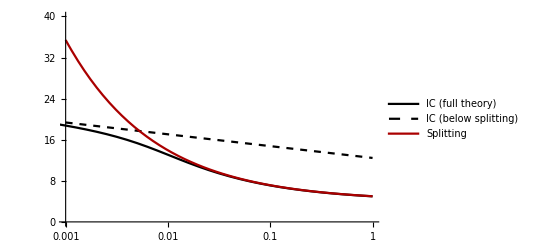

```mathematica
Show[
ListLogLinearPlot[{LambdaStop},Joined->True,PlotStyle->{Black,Gray},PlotRange->{{10^-3,1},{0,40}},PlotLegends->{"IC (full theory)"}],
LogLinearPlot[{LambdaStopLow,LambdaSplit+2lint},{ϵ,10^-3,1},PlotStyle->{{Black,Dashed},Darker@Red},
PlotLegends->{"IC (below splitting)","Splitting"}]
]
```

## Numerics for interrupted coarsening and splitting thresholds

### Continuation

Fixing the value of the source strength ϵ, a pseudo-arclength continuation of an elementary pattern on a domain with length L = Lambda/2 is performed for the finite-differences equations for the elementary stationary pattern.
This procedure is repeated for a list of different source strengths ϵ.

The continuation is started at the length L=π/qo, where qo denotes the wavenumber of the fastest-growing mode around the homogeneous steady state in the limit ϵ=0.

```mathematica
qo=Sqrt[Sqrt[T/Dρ]-1]/Dc/.params;
N@qo
```

2.46395

For low source strengths ϵ, the thresholds occur at large domain length.
Therefore, a fine discretization is necessary.

```mathematica
fdSetupLow=setupFiniteDifferenceEqs[400];
```

Current ϵ: 0.001

FindRoot::precw: The precision of the argument function ({{0.001 (1-ⅇ^a[«1»])+5 (98420.4 (Times[«2»]+Times[«2»]+c[«1»]+Times[«2»])+24605.1 (Times[«2»]+a[«1»]) (Times[«2»]+Times[«2»]+c[«1»]+Times[«2»])),«9»,«390»},{ⅇ^a[1]-c[1]+98420.4 (-c[1]+c[2]),«9»,«390»}}) is less than WorkingPrecision (100.).

Initial stationary pattern found. Start continuation.

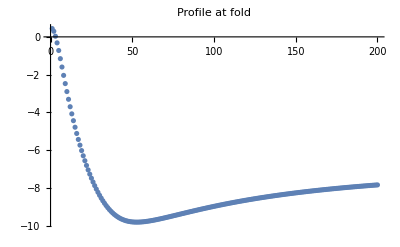

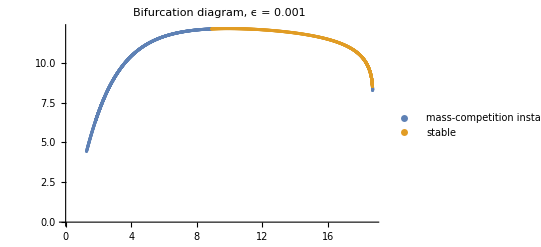

Current ϵ: 0.00316228

FindRoot::precw: The precision of the argument function ({{0.00316228 (1-ⅇ^a[«1»])+5 (98420.4 (Times[«2»]+Times[«2»]+c[«1»]+Times[«2»])+24605.1 (Times[«2»]+a[«1»]) (Times[«2»]+Times[«2»]+c[«1»]+Times[«2»])),«9»,«390»},{ⅇ^a[1]-c[1]+98420.4 (-c[1]+c[2]),«9»,«390»}}) is less than WorkingPrecision (100.).

Initial stationary pattern found. Start continuation.

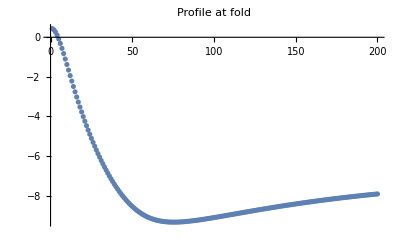

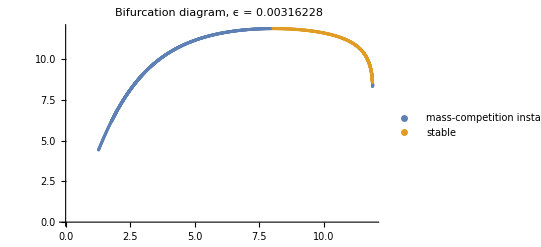

```mathematica
contSweepLow=Block[{
ps,(*current parameters*)
initRun,(*initial solution of PDE*)
initSol,(*initial stationary solution of the finite-differences equations*)
steadyStateCurve,(*continuation result*)
Sfold,(*domain length at fold bifurcation*)
SfoldInd,(*corresponding list index*)
stabList(*list of stability result for the stationary states along the branch of the continuation*)
},
Table[(*sweep over different source strengths ϵ*)
ps=Join[{ϵ->ϵIter},DeleteCases[params,(ϵ->_)|(L->_)]];
Print["Current ϵ: ",ϵIter];

initRun=runKSSim[
Join[{L->Pi/qo},ps],
{(rhoStat/.x->#/.params)&,(Sqrt[3p Dρ/T]/.params)&},
time/.ps,
"GridPoints"->2000
];

initSol=Block[{a,c},FindRoot[
fdSetupLow["Eqs"]/.Join[{L->Pi/qo},ps],
getInitGuess[fdSetupLow,Join[{L->Pi/qo},ps],initRun],
WorkingPrecision->100,(*higher precision necessary for fine discretization*)
MaxIterations->100
]
];
initSol=(#[[1]]->N[#[[2]]])&/@(List@@@initSol);

Print["Initial stationary pattern found. Start continuation."];
steadyStateCurve=arclengthContinuation[
Flatten@fdSetupLow["Eqs"],
Join[{L->Pi/qo},ps],
initSol,
L,0.01,
"ParamDomain"->{0,1000},
"MaxSteps"->10000,"MaxStepSize"->0.1,
"TangentAlignmentThreshold"->0.99,
"TerminateAtFold"->True
];
(*fold position*)
Sfold=Max[steadyStateCurve["CurveData"][[All,1,-1]]];
SfoldInd=First@First@Position[steadyStateCurve["CurveData"][[All,1,-1]],Max[steadyStateCurve["CurveData"][[All,1,-1]]]];

(*stability of the stationary patterns along the branch*)
stabList=Table[Block[{
sol=steadyStateCurve["CurveData"][[ind,1]],
jac,
evals
},

jac=constructGluedJacobian[fdSetupLow,Join[{L->(sol[[-1]])},ps],Thread[fdSetupLow["Vars"]->sol[[;;-2]]],"Reverse"->True];

evals=SortBy[Eigenvalues[jac],Re[#]&];
{
sol[[-1]],(*length*)
evals[[-1]],(*eigenvalue with largest real part*)
sol 
}
],{ind,SfoldInd}];

Print[ListPlot[steadyStateCurve["CurveData"][[SfoldInd,1,;;200]],PlotRange->All,PlotLabel->"Profile at fold"]];
Print[ListPlot[DeleteCases[{
{#[[-1,-1]],#[[-1,1]]-#[[-1,200]]}&/@Select[stabList,Re[#[[2]]]>0&],
{#[[-1,-1]],#[[-1,1]]-#[[-1,200]]}&/@Select[stabList,Re[#[[2]]]<0&]
},{}],PlotLegends->DeleteCases[Transpose@{{"mass-competition instability", "stable"},{
Select[stabList,Re[#[[2]]]>0&],
Select[stabList,Re[#[[2]]]<0&]
}},{_,{}}][[All,1]],PlotLabel->("Bifurcation diagram, ϵ = "<>ToString[ϵIter])]];

{
ϵIter,
Sfold,
stabList
},
{ϵIter,10^Range[-3,-2.5,0.5]}]
];
```

For larger source strengths ϵ, the thresholds occur at lower domain lengths.
Therefore, a coarser discretization is sufficient.

```mathematica
fdSetup=setupFiniteDifferenceEqs[200];
```

Current ϵ: 0.01

Initial stationary pattern found. Start continuation.

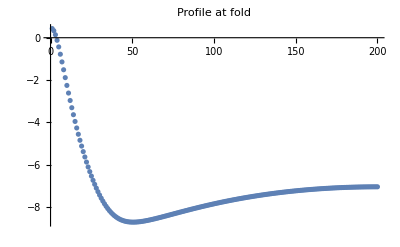

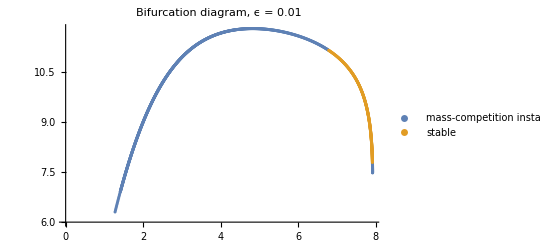

Current ϵ: 0.0316228

Initial stationary pattern found. Start continuation.

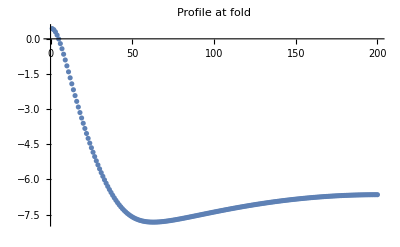

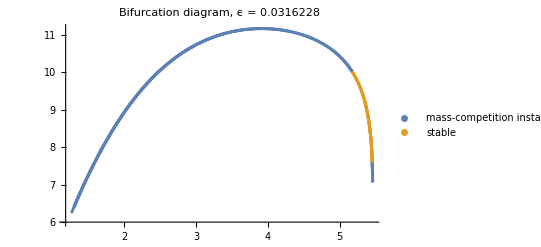

Current ϵ: 0.1

Initial stationary pattern found. Start continuation.

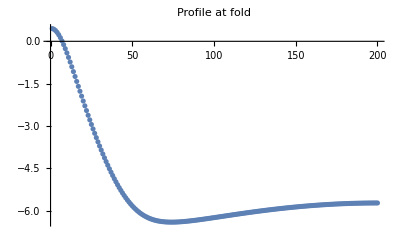

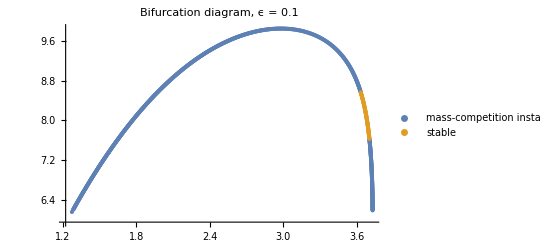

Current ϵ: 0.316228

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

Initial stationary pattern found. Start continuation.

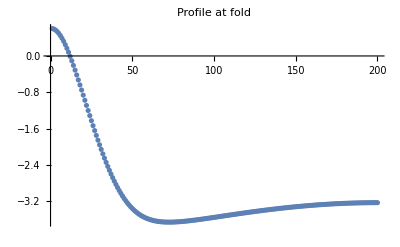

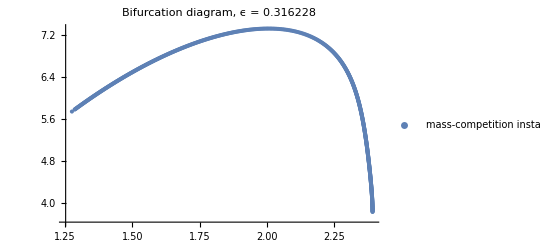

Current ϵ: 1.

Initial stationary pattern found. Start continuation.

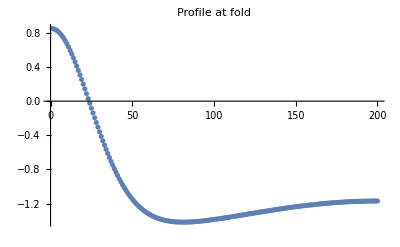

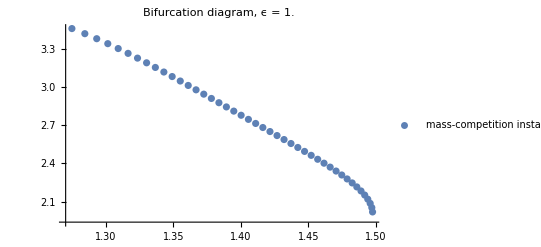

```mathematica
contSweep=Block[{
ps,(*current parameters*)
initRun,(*initial solution of PDE*)
initSol,(*initial stationary solution of the finite-differences equations*)
steadyStateCurve,(*continuation result*)
Sfold,(*domain length at fold bifurcation*)
SfoldInd,(*corresponding list index*)
stabList(*list of stability result for the stationary states along the branch of the continuation*)
},
Table[(*sweep over different source strengths ϵ*)
ps=Join[{ϵ->ϵIter},DeleteCases[params,(ϵ->_)|(L->_)]];
Print["Current ϵ: ",ϵIter];

initRun=runKSSim[
Join[{L->Pi/qo},ps],
{(rhoStat/.x->#/.params)&,(Sqrt[3p Dρ/T]/.params)&},
time/.ps,
"GridPoints"->2000
];

initSol=Block[{a,c},FindRoot[
fdSetup["Eqs"]/.Join[{L->Pi/qo},ps],
getInitGuess[fdSetup,Join[{L->Pi/qo},ps],initRun],
MaxIterations->100
]
];

Print["Initial stationary pattern found. Start continuation."];
steadyStateCurve=arclengthContinuation[
Flatten@fdSetup["Eqs"],
Join[{L->Pi/qo},ps],
initSol,
L,0.01,
"ParamDomain"->{0,1000},
"MaxSteps"->10000,"MaxStepSize"->0.1,
"TangentAlignmentThreshold"->0.99,
"TerminateAtFold"->True
];
(*fold position*)
Sfold=Max[steadyStateCurve["CurveData"][[All,1,-1]]];
SfoldInd=First@First@Position[steadyStateCurve["CurveData"][[All,1,-1]],Max[steadyStateCurve["CurveData"][[All,1,-1]]]];

(*stability of the stationary patterns along the branch*)
stabList=Table[Block[{
sol=steadyStateCurve["CurveData"][[ind,1]],
jac,
evals
},

jac=constructGluedJacobian[fdSetup,Join[{L->(sol[[-1]])},ps],Thread[fdSetup["Vars"]->sol[[;;-2]]],"Reverse"->True];

evals=SortBy[Eigenvalues[jac],Re[#]&];
{
sol[[-1]],(*length*)
evals[[-1]],(*eigenvalue with largest real part*)
sol 
}
],{ind,SfoldInd}];

Print[ListPlot[steadyStateCurve["CurveData"][[SfoldInd,1,;;200]],PlotRange->All,PlotLabel->"Profile at fold"]];
Print[ListPlot[DeleteCases[{
{#[[-1,-1]],#[[-1,1]]-#[[-1,200]]}&/@Select[stabList,Re[#[[2]]]>0&],
{#[[-1,-1]],#[[-1,1]]-#[[-1,200]]}&/@Select[stabList,Re[#[[2]]]<0&]
},{}],PlotLegends->DeleteCases[Transpose@{{"mass-competition instability", "stable"},{
Select[stabList,Re[#[[2]]]>0&],
Select[stabList,Re[#[[2]]]<0&]
}},{_,{}}][[All,1]],PlotLabel->("Bifurcation diagram, ϵ = "<>ToString[ϵIter])]];

{
ϵIter,
Sfold,
stabList
},
{ϵIter,10^Range[-2,0,0.5]}]
];
```

```mathematica
thresholds={#[[1]],Function[indList,If[indList==={},I,With[{ind=indList[[1,1]]},#[[3,ind-1,1]]+(#[[3,ind,1]]-#[[3,ind-1,1]])Abs[Re@#[[3,ind-1,2]]]/(Abs[Re@#[[3,ind-1,2]]]+Abs[Re@#[[3,ind,2]]])]]]@Select[Transpose@{Range[Length@#[[3]]],#[[3]]},Function[x,Re[x[[2,2]]]<0]],#[[2]]}&/@Join[contSweepLow,contSweep];
```

```mathematica
{#[[1]],2#[[2]],2#[[3]]}&/@thresholds
```

{{0.001,17.8158,37.4748},{0.00316228,16.0569,23.7758},{0.01,13.5624,15.8405},{0.0316228,10.3565,10.9119},{0.1,7.26453,7.45834},{0.316228,2 ⅈ,4.785},{1.,2 ⅈ,2.99477}}

```mathematica
TableForm[Join[{{"ϵ","Lambda_stop","Lambda_split"}},{#[[1]],2#[[2]],2#[[3]]}&/@thresholds]/.{2 ⅈ->"failed"}]
```

ϵ | Lambda_stop | Lambda_split
0.001 | 17.8158 | 37.4748
0.00316228 | 16.0569 | 23.7758
0.01 | 13.5624 | 15.8405
0.0316228 | 10.3565 | 10.9119
0.1 | 7.26453 | 7.45834
0.316228 | failed | 4.785
1. | failed | 2.99477

### Results

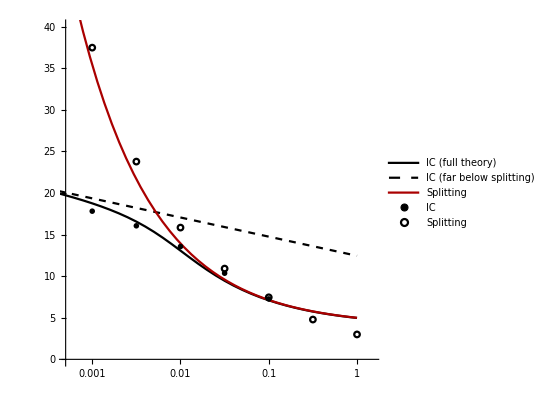

```mathematica
Show[
ListLogLinearPlot[{LambdaStop},Joined->True,PlotStyle->{Black,Gray},PlotRange->{{5 10^-4,1.5},{0,40}},PlotLegends->{"IC (full theory)"},AspectRatio->1],
LogLinearPlot[{LambdaStopLow,LambdaSplit+2lint},{ϵ,10^-4,1},PlotStyle->{{Black,Dashed},Darker@Red},
PlotLegends->{"IC (far below splitting)","Splitting"}],
ListLogLinearPlot[{{#[[1]],2*#[[2]]}&/@thresholds,
{#[[1]],2*#[[3]]}&/@thresholds},PlotMarkers->{{Graphics[{Black,Disk[]}],0.04},{Graphics[{Black,Circle[]}],0.04}},PlotLegends->{"IC","Splitting"}]
]
```

#### Plot stationary patterns

```mathematica
ϵInd=1;
Manipulate[ListLogPlot[{Transpose@{fdSetup["UnitGrid"]*contSweep[[ϵInd,3,Floor@i,3,-1]],Exp@contSweep[[ϵInd,3,Floor@i,3,;;200]]},
Transpose@{fdSetup["UnitGrid"]*contSweep[[ϵInd,3,Floor@i,3,-1]],Exp[T/Dρ(Dρ/T contSweep[[ϵInd,3,Floor@i,3,;;200]] -contSweep[[ϵInd,3,Floor@i,3,201;;400]])/.params]}}],{i,1,Length@contSweep[[ϵInd,3]]}]
```